```mathematica
M=With[{n=50},Table[If[RandomReal[]<.04,RandomInteger[{1,10}],0],n,n]];
```

```mathematica
G=AdjacencyGraph[M]
```

-Graphics-

```mathematica
totals=Total[M,{2}];
Ordering[totals]
```

{1,15,26,33,39,42,50,25,38,6,24,36,49,8,27,4,10,32,9,23,30,40,43,46,48,19,2,11,31,35,45,3,20,18,28,44,5,13,21,29,37,41,17,47,12,14,22,7,16,34}

```mathematica
Subscript[g, i_]:=Module[{out,in,neighbors,verts},
out=Flatten@Position[M[[i]],_?Positive];
in=Flatten@Position[M[[All,i]],_?Positive];
neighbors=Union[out,in];
verts=Prepend[neighbors,i];
AdjacencyGraph[M[[verts,verts]],VertexLabels->Placed["Name",Tooltip]]]
```

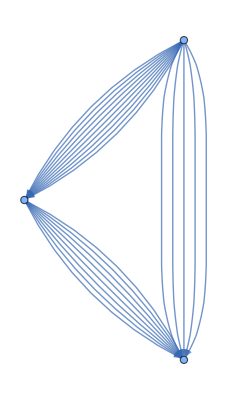

```mathematica
Subscript[g, 10]
```

```mathematica
GraphHub[Subgraph[G,#]]&/@FindGraphCommunities[G]
```

{{47},{3},{11,19,29,40},{34},{7,18},{12},{23},{37},{39},{50}}

```mathematica
CommunityGraphPlot[G,EdgeStyle->LightGray]
```

-Graphics-

```mathematica
Partition[HighlightGraph[Subgraph[G,#],GraphHub[Subgraph[G,#]]]&/@FindGraphCommunities[G],3,3]//GraphicsGrid
```

-Graphics-